# Notebook for computing the spectrum of linearized MKdV operator.

This notebook computes the spectrum of the linearization about a traveling wave solution to a generalized KdV, in this case MKdV. Specifically we are finding traveling wave solutions to 

in particular the solution , where  solves 
 
in this particular instance the parameter values are , giving a period of roughly     This is the focusing case of MKdV.  
In the code snippet below Abel gives the polynomial in the quadrature . The traveling wave equation is integrated to give the  traveling wave profile. The function Pot(x) returns the potential for the linearized problem.

```mathematica
(* Notebook for computing the spectrum of the linearization around a traveling wave solution to MKdV.*)
(* This generates the traveling wave solutions to gKdV. *)
(* Abel gives the polynomial Subscript[ϕ, x]^2 = Abel[ϕ] giving the solution via quadrature. *)
(* Subscript[u, t] + Subscript[u, xxx] + (u^p)_x = 0 *)
(* p=2 KdV. p=3 MKdV *)
```

```mathematica
p = 3;
c=1;
En = 2/5;
a = 1/5;
Abel[ϕ_,E_,a_,c_] := 2 E + 2 a ϕ + c ϕ^2 - 2ϕ^(p+1)/(p+1)
RootList=N[x /.Solve[Abel[x,En,a,c]==0,x,Reals,WorkingPrecision->30]];
root2=RootList[[Dimensions[RootList][[1]]]];
root1=RootList[[Dimensions[RootList][[1]]-1]];
avg = (root2+root1)/2;
rad = (root2-root1)/2;
ReducedPoly = PolynomialQuotient[Abel[x,En,a,c],(x-root1)(root2-x),x];
Period = NIntegrate[1/Sqrt[ReducedPoly /. x -> avg + rad Sin[Θ]],{Θ,-Pi,Pi}];
WaveProfile = NDSolve[{y''[x]==a + c y[x] - y[x]^(p)  ,y[0]==root2,y'[0]==0},y,{x,0,2 Period},AccuracyGoal->13,PrecisionGoal->13];
Pot[x_] := Evaluate[(p y[x]^(p-1) - c) /. WaveProfile ][[1]]
```

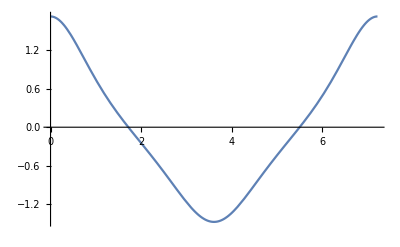

```mathematica
Plot[Evaluate[y[x]/. WaveProfile],{x,0,Period}]
```

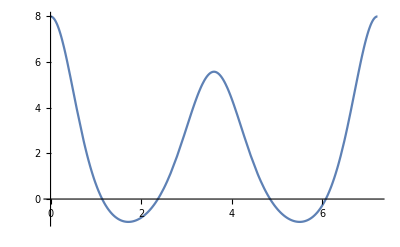

```mathematica
Plot[Pot[x],{x,0,Period}]
```

The code snippet below solves the ODE defining the linearized operator as well as the derivative of this ODE with respect to the eigenvalue parameter λ. This will allow us to generate the monodromy matrix as well as the derivative of the monodromy matrix with respect to the eigenvalue parameter λ. The derivatives are necessary for computing the bifurcation index.

```mathematica
SolMonodromy[l_] := NDSolve[{r1'''[x] + (Pot[x]) r1'[x] - l r1[x]==0,dr1'''[x] + (Pot[x]) dr1'[x] - l dr1[x]-r1[x]==0,r2'''[x] + (Pot[x] ) r2'[x] - l r2[x]==0,dr2'''[x] + (Pot[x] ) dr2'[x] - l dr2[x]- r2[x]==0,r3'''[x] + (Pot[x]) r3'[x] - l r3[x]==0 ,dr3'''[x] + (Pot[x]) dr3'[x] - l dr3[x]-r3[x]==0 ,r1[0]==1,r1'[0]==0,r1''[0]==0,r2[0]==0,r2'[0]==1,r2''[0]==0,r3[0]==0,r3'[0]==0,r3''[0]==1,dr1[0]==0,dr1'[0]==0,dr1''[0]==0,dr2[0]==0,dr2'[0]==0,dr2''[0]==0,dr3[0]==0,dr3'[0]==0,dr3''[0]==0},{r1,r2,r3,dr1,dr2,dr3},{x,0,Period}];
mono[l_] := Evaluate[{{r1[Period],r2[Period],r3[Period]},{r1'[Period],r2'[Period],r3'[Period]},{r1''[Period],r2''[Period],r3''[Period]}}] /. SolMonodromy[l][[1]]
```

The monodromy matrix at λ=0 should have μ=1 as an eigenvalue of geometric multiplicity 2 and algebraic multiplicity 3. The relative error is about .1%.

```mathematica
MatrixForm[mono[0]]
```

(1. | 27.8553 | -4.8689×10^-7
0. | 1. | -1.6757×10^-8
0. | -50.4383 | 1.)

```mathematica
Eigenvalues[%]
```

{1.00092,1.,0.999081}

The code snippets below compute the characteristic polynomial of the monodromy matrix (CharPoly[λ]), the complex Floquet discriminant (FloqD), the derivative with respect to λ of the  Floquet discriminant (FloqDp), the discriminant of the characteristic polynomial (Disco) and the bifurcation index (BifIndex)

```mathematica
CharPoly[l_] := CharacteristicPolynomial[mono[l] , μ ];
MonoRoots[l_] := μ /. Solve[CharPoly[l]==0,μ];
FloqD[l_] := (Evaluate[r1[Period] + r2'[Period] + r3''[Period]]/. SolMonodromy[l])[[1]]
FloqDp[l_] := (Evaluate[dr1[Period] + dr2'[Period] + dr3''[Period]]/. SolMonodromy[l])[[1]]
Disco[λ_] := Evaluate[(-27-4 Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^3+18 Conjugate[r1[Period]+r2'[Period]+r3''[Period]] (r1[Period]+r2'[Period]+r3''[Period])+Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^2 (r1[Period]+r2'[Period]+r3''[Period])^2-4 (r1[Period]+r2'[Period]+r3''[Period])^3)]/. SolMonodromy[λ][[1]]
BifIndex[l_] := Module[{FF = FloqD[l],FP=FloqDp[l],FPC = Conjugate[FP]},FP^3 + Conjugate[FP]^3 + FF FP Conjugate[FP]^2 + Conjugate[FF] Conjugate[FP] FP^2 ]
```

The plot below depicts the bifurcation index along the imaginary axis (by symmetry this is a real quantity for λ purely imaginary. The plot is turned 90° so that we can see where the plot crosses the y-axis. Those crossings mark bifurcation points.

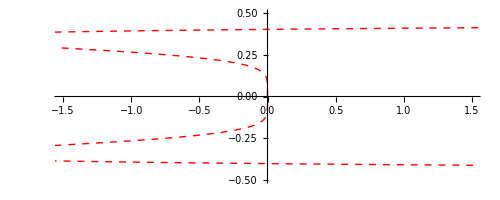

```mathematica
BifIndexPlot=ParametricPlot[{BifIndex[I l],l},{l,-.5,0.50},PlotRange->{{-1.5,1.5},{-0.5,0.5}},PlotStyle->{Red,Thick,Dashed}]
```

```mathematica
Discrim[l_] := Re[Discriminant[CharPoly[l],μ]]
```

```mathematica
Mult[λ_] := If[Discrim[λ]>0,.005,.005I]
```

```mathematica
Discrim[5I]
```

1.74331×10^14

```mathematica
Mult[I]
```

0.005

```mathematica
Mult[4.0I]
```

0.005

```mathematica
MultiplicityGraph=ParametricPlot[{{0.00002(1-Sign[Discrim[l I]])/2+ I (1+Sign[Discrim[I l]]),l},{-0.00002(1-Sign[Discrim[l I]])/2+ I (1+Sign[Discrim[I l]]),l}},{l,-0.4,0.4},PlotStyle->{{Thick,Magenta},{Thick,Magenta}},PlotRange->{-1,1},PlotPoints->100]
```

-Graphics-

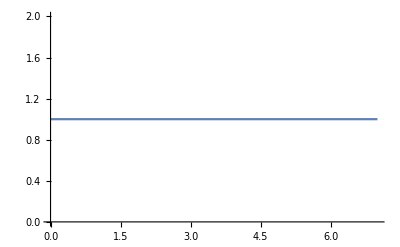

```mathematica
Plot[Sign[Discrim[I λ]],{λ,0,7}]
```

```mathematica
Discrim[I]
```

5.17783×10^7

```mathematica
Discrim[0]
```

1.25176×10^-9

```mathematica
(* Deltoid = Locus of points where the (complex) Floquet discriminant has three eigenvalues on the unit circle along the imaginary axis *)
```

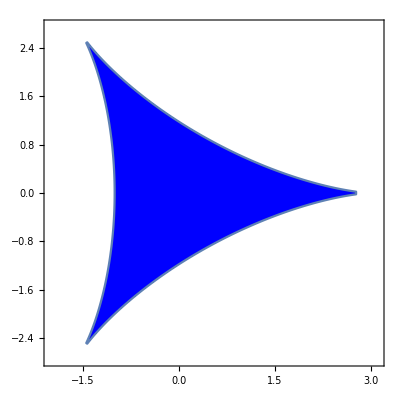

```mathematica
Deltoid1=RegionPlot[-27+18 a^2-8 a^3+a^4+18 b^2+24 a b^2+2 a^2 b^2+b^4<0,{a,-3,3.5},{b,-3.25,3.25},PlotPoints->100,PlotRange->{{-2,3.1},{-2.75,2.75}},PlotStyle->Blue]
```

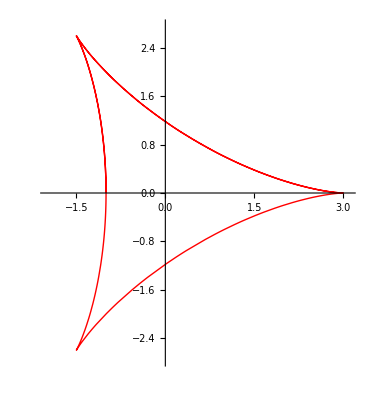

```mathematica
(* This is the Cartesian *)
Astroid[a_,b_,r_] := ParametricPlot[ -r{(a-b) Cos[t] + b Cos[(a-b)/b t],(a-b) Sin[t] + b Sin[(a-b)/b t]},{t,0,6Pi},PlotStyle->{Thick,Red},PlotRange->{{-2,3.1},{-2.75,2.75}}]  
Deltoid2=Astroid[1,2,1]
```

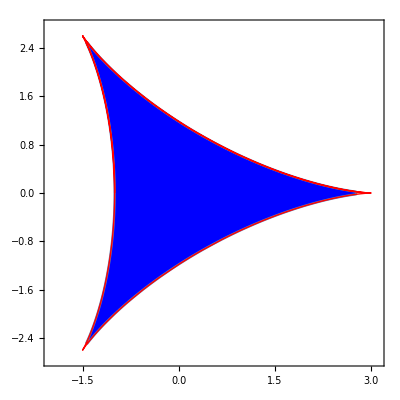

```mathematica
Deltoid3=Show[Deltoid1,Deltoid2]
```

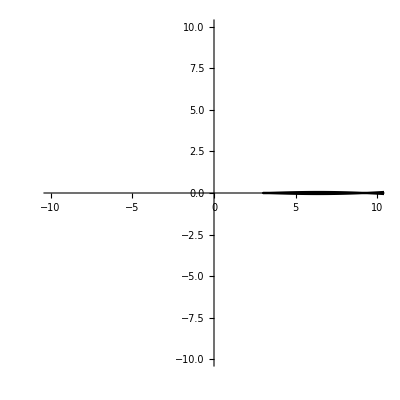

```mathematica
FDPlot=ParametricPlot[{Re[FloqD[I λ]],Im[FloqD[I λ]]},{λ,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->Black]
```

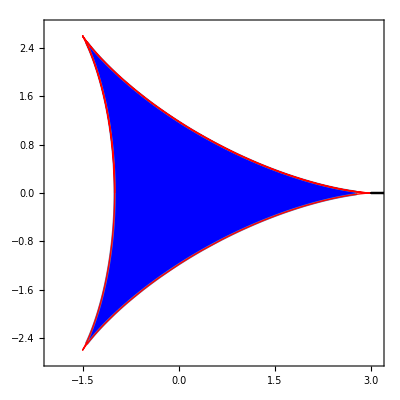

```mathematica
Delt2=Show[Deltoid3,FDPlot]
```

```mathematica
L = Period;
NM = 25;
dx = L/NM;diag = Table[2*Pi*I*1.0(NM-j)/Period,{j,1,2*NM+1}];D1=DiagonalMatrix[diag];
FM = Table[NIntegrate[Exp[2 Pi I k x/Period] Pot[x]/Period,{x,0,Period},AccuracyGoal->15],{k,-2*NM,2*NM}];
FCol = Table[FM[[2NM+2-i]],{i,1,2*NM+1}];
FRow = Table[FM[[i]],{i,2*NM+1,4*NM+1}];
Pot2[x_] := Re[Sum[FM[[k]] Exp[2 Pi I (k-(2*NM+1)) x/Period],{k,1,4*NM+1}]];
PotM = ToeplitzMatrix[Re[FCol],Re[FRow]];
D3=D1.D1.D1;D2=D1.D1;D0=IdentityMatrix[2NM+1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.2683×10^-13-3.45486×10^-15 ⅈ and 3.86313×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.26685×10^-13-1.46343×10^-14 ⅈ and 3.18174×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.9832830096543912533590577804918220488646475943572689004668063717}. NIntegrate obtained 2.51005×10^-13-8.36809×10^-15 ⅈ and 4.18396×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47902×10^-13-7.53781×10^-15 ⅈ and 1.74333×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.1051412149983921223097531602093650773723908925516568046987231355}. NIntegrate obtained 3.08558×10^-13-1.7421×10^-15 ⅈ and 3.70578×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.0006913252464446030267605670250566373308568832167786410991539015}. NIntegrate obtained 3.80075×10^-13-8.06646×10^-15 ⅈ and 3.52503×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.2683×10^-13-3.45486×10^-15 ⅈ,2.26685×10^-13-1.46343×10^-14 ⅈ,2.51005×10^-13-8.36809×10^-15 ⅈ,2.47902×10^-13-7.53781×10^-15 ⅈ,2.67369×10^-13-1.1934×10^-14 ⅈ,2.74123×10^-13-5.57817×10^-15 ⅈ,2.89058×10^-13-6.93293×10^-15 ⅈ,3.08558×10^-13-1.7421×10^-15 ⅈ,3.22728×10^-13+4.06793×10^-16 ⅈ,3.41502×10^-13-7.21385×10^-15 ⅈ,3.62914×10^-13-5.4054×10^-15 ⅈ,3.80075×10^-13-8.06646×10^-15 ⅈ,4.05593×10^-13-1.13898×10^-14 ⅈ,4.305×10^-13-7.07941×10^-15 ⅈ,4.58942×10^-13-8.60863×10^-15 ⅈ,4.87828×10^-13-1.27252×10^-14 ⅈ,5.44236×10^-13-1.10641×10^-14 ⅈ,6.38204×10^-13-3.19102×10^-15 ⅈ,8.95826×10^-13-1.56984×10^-14 ⅈ,1.53862×10^-12+6.608×10^-15 ⅈ,3.24214×10^-12-1.59209×10^-14 ⅈ,7.88895×10^-12+2.93255×10^-15 ⅈ,2.07456×10^-11-4.26091×10^-16 ⅈ,5.56298×10^-11-5.75657×10^-15 ⅈ,1.53888×10^-10+1.13×10^-14 ⅈ,4.16988×10^-10-2.32269×10^-15 ⅈ,1.16506×10^-9-7.55364×10^-16 ⅈ,3.13457×10^-9-2.90575×10^-14 ⅈ,8.80628×10^-9-1.49238×10^-14 ⅈ,2.33811×10^-8-6.04393×10^-14 ⅈ,6.61887×10^-8-1.79485×10^-14 ⅈ,1.72409×10^-7-4.46448×10^-14 ⅈ,4.94019×10^-7-2.68092×10^-14 ⅈ,1.25231×10^-6-2.11431×10^-14 ⅈ,3.65753×10^-6-3.61103×10^-14 ⅈ,8.91661×10^-6-1.44318×10^-14 ⅈ,0.0000268218-4.9206×10^-14 ⅈ,0.0000617856-6.37086×10^-14 ⅈ,0.000194382-1.41773×10^-13 ⅈ,0.000411996-1.97615×10^-13 ⅈ,0.00138651-5.52062×10^-13 ⅈ,0.00259512-9.26843×10^-13 ⅈ,0.00965394-3.10604×10^-12 ⅈ,0.0149351-4.33809×10^-12 ⅈ,0.0644148-1.55485×10^-11 ⅈ,0.07334-1.48097×10^-11 ⅈ,0.39277-6.2982×10^-11 ⅈ,0.256972-3.08825×10^-11 ⅈ,1.87457-1.50864×10^-10 ⅈ,0.256311-1.01989×10^-11 ⅈ,2.09324,0.256311+1.01989×10^-11 ⅈ,1.87457+1.50864×10^-10 ⅈ,0.256972+3.08825×10^-11 ⅈ,0.39277+6.2982×10^-11 ⅈ,0.07334+1.48097×10^-11 ⅈ,0.0644148+1.55485×10^-11 ⅈ,0.0149351+4.33809×10^-12 ⅈ,0.00965394+3.10604×10^-12 ⅈ,0.00259512+9.26843×10^-13 ⅈ,0.00138651+5.52062×10^-13 ⅈ,0.000411996+1.97615×10^-13 ⅈ,0.000194382+1.41773×10^-13 ⅈ,0.0000617856+6.37086×10^-14 ⅈ,0.0000268218+4.9206×10^-14 ⅈ,8.91661×10^-6+1.44318×10^-14 ⅈ,3.65753×10^-6+3.61103×10^-14 ⅈ,1.25231×10^-6+2.11431×10^-14 ⅈ,4.94019×10^-7+2.68092×10^-14 ⅈ,1.72409×10^-7+4.46448×10^-14 ⅈ,6.61887×10^-8+1.79485×10^-14 ⅈ,2.33811×10^-8+6.04393×10^-14 ⅈ,8.80628×10^-9+1.49238×10^-14 ⅈ,3.13457×10^-9+2.90575×10^-14 ⅈ,1.16506×10^-9+7.55364×10^-16 ⅈ,4.16988×10^-10+2.32269×10^-15 ⅈ,1.53888×10^-10-1.13×10^-14 ⅈ,5.56298×10^-11+5.75657×10^-15 ⅈ,2.07456×10^-11+4.26091×10^-16 ⅈ,7.88895×10^-12-2.93255×10^-15 ⅈ,3.24214×10^-12+1.59209×10^-14 ⅈ,1.53862×10^-12-6.608×10^-15 ⅈ,8.95826×10^-13+1.56984×10^-14 ⅈ,6.38204×10^-13+3.19102×10^-15 ⅈ,5.44236×10^-13+1.10641×10^-14 ⅈ,4.87828×10^-13+1.27252×10^-14 ⅈ,4.58942×10^-13+8.60863×10^-15 ⅈ,4.305×10^-13+7.07941×10^-15 ⅈ,4.05593×10^-13+1.13898×10^-14 ⅈ,3.80075×10^-13+8.06646×10^-15 ⅈ,3.62914×10^-13+5.4054×10^-15 ⅈ,3.41502×10^-13+7.21385×10^-15 ⅈ,3.22728×10^-13-4.06793×10^-16 ⅈ,3.08558×10^-13+1.7421×10^-15 ⅈ,2.89058×10^-13+6.93293×10^-15 ⅈ,2.74123×10^-13+5.57817×10^-15 ⅈ,2.67369×10^-13+1.1934×10^-14 ⅈ,2.47902×10^-13+7.53781×10^-15 ⅈ,2.51005×10^-13+8.36809×10^-15 ⅈ,2.26685×10^-13+1.46343×10^-14 ⅈ,2.2683×10^-13+3.45486×10^-15 ⅈ}

Eig[q] and Eig2[q] compute the spectrum with quasi-periodic boundary conditions v(L) = exp(2 π i q/L) v(0). Eig computes the spectrum of the linearized operator and Eig2 computes the spectrum of the adjoint. These should be isospectral. At q=0 both show have a triple eigenvalue of 0. In both cases the zero eigenvalues of of order 2 x10^-5

```mathematica
Eig[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 +  PotM.(D1 - I q D0)];
Eig2[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 + (D1 - I q D0). PotM];
```

```mathematica
Chop[Eig[0.0]]
Chop[Eig2[0.0]]
```

{0.+11553.5 ⅈ,0.+10267.7 ⅈ,0.-9080.84 ⅈ,0.+9080.15 ⅈ,0.-7989.02 ⅈ,0.+7988.34 ⅈ,0.-6987.63 ⅈ,0.+6987.6 ⅈ,0.-6074.02 ⅈ,0.+6074. ⅈ,0.-5243.56 ⅈ,0.+5243.56 ⅈ,0.-4492.32 ⅈ,0.+4492.32 ⅈ,0.-3816.32 ⅈ,0.+3816.32 ⅈ,0.-3211.61 ⅈ,0.+3211.61 ⅈ,0.-2674.21 ⅈ,0.+2674.21 ⅈ,0.-2200.17 ⅈ,0.+2200.17 ⅈ,0.-1785.53 ⅈ,0.+1785.53 ⅈ,0.-1426.33 ⅈ,0.+1426.33 ⅈ,0.-1118.61 ⅈ,0.+1118.61 ⅈ,0.-858.414 ⅈ,0.+858.414 ⅈ,0.-641.776 ⅈ,0.+641.776 ⅈ,0.-464.737 ⅈ,0.+464.737 ⅈ,0.+323.339 ⅈ,0.-323.339 ⅈ,0.+213.62 ⅈ,0.-213.62 ⅈ,0.+131.62 ⅈ,0.-131.62 ⅈ,0.+73.3777 ⅈ,0.-73.3777 ⅈ,0.+34.9289 ⅈ,0.-34.9289 ⅈ,0.+12.291 ⅈ,0.-12.291 ⅈ,0.-0.742695 ⅈ,0.+0.742695 ⅈ,0.0000258534-1.95256×10^-9 ⅈ,-0.0000258534+1.95257×10^-9 ⅈ,0}

{0.+11553.5 ⅈ,0.+10267.7 ⅈ,0.-9080.84 ⅈ,0.+9080.15 ⅈ,0.-7989.02 ⅈ,0.+7988.34 ⅈ,0.-6987.63 ⅈ,0.+6987.6 ⅈ,0.-6074.02 ⅈ,0.+6074. ⅈ,0.-5243.56 ⅈ,0.+5243.56 ⅈ,0.-4492.32 ⅈ,0.+4492.32 ⅈ,0.-3816.32 ⅈ,0.+3816.32 ⅈ,0.-3211.61 ⅈ,0.+3211.61 ⅈ,0.-2674.21 ⅈ,0.+2674.21 ⅈ,0.-2200.17 ⅈ,0.+2200.17 ⅈ,0.-1785.53 ⅈ,0.+1785.53 ⅈ,0.-1426.33 ⅈ,0.+1426.33 ⅈ,0.-1118.61 ⅈ,0.+1118.61 ⅈ,0.-858.414 ⅈ,0.+858.414 ⅈ,0.-641.776 ⅈ,0.+641.776 ⅈ,0.-464.737 ⅈ,0.+464.737 ⅈ,0.-323.339 ⅈ,0.+323.339 ⅈ,0.+213.62 ⅈ,0.-213.62 ⅈ,0.-131.62 ⅈ,0.+131.62 ⅈ,0.-73.3777 ⅈ,0.+73.3777 ⅈ,0.-34.9289 ⅈ,0.+34.9289 ⅈ,0.+12.291 ⅈ,0.-12.291 ⅈ,0.+0.742695 ⅈ,0.-0.742695 ⅈ,0.0000258568+1.44389×10^-9 ⅈ,-0.0000258568-1.44396×10^-9 ⅈ,0}

```mathematica
frame=Plot[0,{x,-1.5,1.5},PlotRange->{-.5,.5}];
l = {}
Do[l=Join[l,Eig[Q]],{Q,-.5,.5,.0001}]
Dimensions[l]
```

{510051}

Find the largest real part to set the scale appropriately.

```mathematica
Max[Re[l]]
```

1.10578

```mathematica
MKdVHotDog= Show[frame,ComplexListPlot[l,PlotStyle->{Blue,PointSize[Small]}],BifIndexPlot]
```

-Graphics-

```mathematica
Export["mKdVHotDog.pdf",MKdVHotDog]
```

mKdVHotDog.pdf

```mathematica
Export["mKdVHotDog.png",MKdVHotDog]
```

mKdVHotDog.png